# Type II model

## Modelling the Hamiltonian in Eq. (11) in Chiral anomaly and longitudinal magnetotransport in type-II Weyl semimetals

```mathematica
x[k_]:=k[[1]]
y[k_]:=k[[2]]
z[k_]:=k[[3]]
```

```mathematica
HI[k_]:=((Cos[y[k]] + Cos[z[k]] - 2) m  - 2 t (Cos[x[k]] - Cos[k0])) PauliMatrix[1] - 2 t Sin[y[k]] PauliMatrix[2] - 2 t Sin[z[k]] PauliMatrix[3]
```

```mathematica
HII[k_]:=HI[k] + γ (Cos[x[k]] - Cos[k0]) PauliMatrix[0]
```

```mathematica
Plot3D[
Eigenvalues[HII[{kx, ky, 0}]/. m->2t/.{ γ->0, t->-0.005, k0->Pi/2}
], {kx, -2, 2}, {ky, -2, 2}]
```

-Graphics3D-

```mathematica
HII[{kx, ky, 0}]/.{ γ->0, m->0.15, t->-0.005, k0->Pi/2}
```

{{0,0.01 Cos[kx]+0.15 (-1+Cos[ky])-(0.+0.01 ⅈ) Sin[ky]},{0.01 Cos[kx]+0.15 (-1+Cos[ky])+(0.+0.01 ⅈ) Sin[ky],0}}

## Plotting

### Fermi surface

```mathematica
Eigenvalues[HII[{kx, ky, 0}]/.m->2t]/.{  t->5/100, k0->Pi/2}
```

{γ Cos[kx]-√2 √(1/80+Cos[kx]/100+1/400 Cos[2 kx]-1/200 Cos[kx-ky]-Cos[ky]/100-1/200 Cos[kx+ky]),γ Cos[kx]+√2 √(1/80+Cos[kx]/100+1/400 Cos[2 kx]-1/200 Cos[kx-ky]-Cos[ky]/100-1/200 Cos[kx+ky])}

```mathematica
Plot3D[γ Cos[kx]-√2 √(1/80+Cos[kx]/100+1/400 Cos[2 kx]-1/200 Cos[kx-ky]-Cos[ky]/100-1/200 Cos[kx+ky])/.γ->3 5/100, {kx,-2,2},{ky,-2,2}]
```

-Graphics3D-

```mathematica
Reduce[γ Cos[kx]-√2 √(1/80+Cos[kx]/100+1/400 Cos[2 kx]-1/200 Cos[kx-ky]-Cos[ky]/100-1/200 Cos[kx+ky])==0&&γ<-15/100, {kx, ky}, Reals]
```

((C[1]|C[2])∈ℤ&&γ<-3/20&&((-2 ArcTan[√((-3+10 γ)/(1+10 γ))]+2 π C[2]<kx<1/2 (-π+4 π C[2])&&(ky==2 ArcTan[√(-((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4))]-2 π C[1]||ky==-2 ArcTan[√(-((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4))]-2 π C[1]))||(1/2 (π+4 π C[2])<kx<2 ArcTan[√((-3+10 γ)/(1+10 γ))]+2 π C[2]&&(ky==2 ArcTan[√(-((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4))]-2 π C[1]||ky==-2 ArcTan[√(-((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4))]-2 π C[1]))))||((C[1]|C[2])∈ℤ&&γ<-3/20&&((kx==-π/2+2 π C[1]&&ky==-2 π C[2])||(kx==π/2+2 π C[1]&&ky==-2 π C[2])))||((C[1]|C[2])∈ℤ&&γ<-3/20&&((kx==-2 ArcTan[√(80 √(γ^2/((-2+200 γ^2)^2))+(6+200 γ^2)/(-2+200 γ^2))]+2 π C[2]&&ky==-π-2 π C[1])||(kx==2 ArcTan[√(80 √(γ^2/((-2+200 γ^2)^2))+(6+200 γ^2)/(-2+200 γ^2))]+2 π C[2]&&ky==-π-2 π C[1])))

```mathematica
%/.{C[1]->0,C[2]->0}
```

(γ<-3/20&&((-2 ArcTan[√((-3+10 γ)/(1+10 γ))]<kx<-π/2&&(ky==2 ArcTan[√(-(((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4)))]||ky==-2 ArcTan[√(-(((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4)))]))||(π/2<kx<2 ArcTan[√((-3+10 γ)/(1+10 γ))]&&(ky==2 ArcTan[√(-(((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4)))]||ky==-2 ArcTan[√(-(((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4)))]))))||(γ<-3/20&&((kx==-π/2&&ky==0)||(kx==π/2&&ky==0)))||(γ<-3/20&&((kx==-2 ArcTan[√(80 √(γ^2/((-2+200 γ^2)^2))+(6+200 γ^2)/(-2+200 γ^2))]&&ky==-π)||(kx==2 ArcTan[√(80 √(γ^2/((-2+200 γ^2)^2))+(6+200 γ^2)/(-2+200 γ^2))]&&ky==-π)))

Plot::plln: Limiting value -2 ArcTan[√((-3-10 γ)/(1-10 γ))] in {kx,-2 ArcTan[√((-3-10 γ)/(1+Times[«2»]))],2 ArcTan[√((-3-10 γ)/(1+Times[«2»]))]} is not a machine-sized real number.

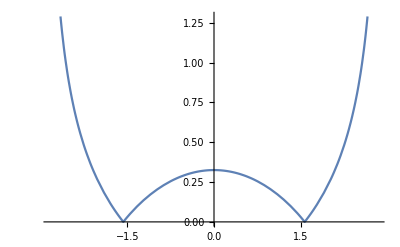

```mathematica
Plot[ 2 ArcTan[√(-(((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4)))], {kx, -2 ArcTan[√((-3-10 γ)/(1-10 γ))], 2 ArcTan[√((-3-10 γ)/(1-10 γ))]}]/.γ->11/100
```

Infinity::indet: Indeterminate expression -9+100 γ^2+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

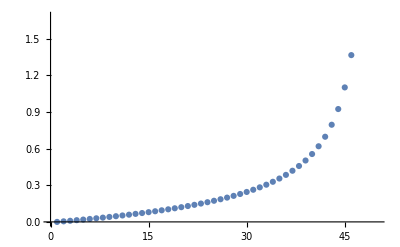

```mathematica
tmp=Subdivide[Pi/2, Pi,50];
ListPlot[Table[2 ArcTan[√(-(((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4)))], {kx,tmp}]/.γ->10.1/100//N//Re]
```

```mathematica
kxlistInner=Subdivide[-Pi/2, Pi/2,50];
kxlistOuter=Subdivide[Pi/2, Pi,50];
gammaList=Table[{γ->i}, {i, {10.1,12,13,14,15, 30}/100}];
fermi[list_]:=Evaluate[Table[2 ArcTan[√(-(((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4)))], {kx,list}]/.gammaList//N//Re]/.Indeterminate->N[Pi];
Export["/home/thorvald/Documents/NTNU/10semester/Thesis/data/fermiLevelTightInner.csv", Transpose[FlattenAt[Join[{kxlistInner//N}, {fermi[kxlistInner]}],2]]]
Export["/home/thorvald/Documents/NTNU/10semester/Thesis/data/fermiLevelTightOuter.csv", Transpose[FlattenAt[Join[{kxlistOuter//N}, {fermi[kxlistOuter]}],2]]]
```

Power::infy: Infinite expression 1/0 encountered.

/home/thorvald/Documents/NTNU/10semester/Thesis/data/fermiLevelTightInner.csv

Infinity::indet: Indeterminate expression -9+100 γ^2+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

/home/thorvald/Documents/NTNU/10semester/Thesis/data/fermiLevelTightOuter.csv

```mathematica
FullSimplify[ 2 ArcTan[√(-((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4))], {{γ, kx}∈Reals, kx>0}]
```

2 ArcTan[Abs[Cos[kx]] √((2-200 γ^2)/(-9+100 γ^2-8 Cos[kx]+(-1+100 γ^2) Cos[2 kx]))]

```mathematica
FullSimplify[ 2 ArcTan[√(-((-1+100 γ^2) (-1+Tan[kx/2]^2)^2)/(-9+100 γ^2-6 Tan[kx/2]^2-200 γ^2 Tan[kx/2]^2-Tan[kx/2]^4+100 γ^2 Tan[kx/2]^4))]/.γ->15/100, {{γ, kx}∈Reals, kx>0}]
```

2 ArcTan[√10 Abs[Cos[kx]] √(1/(27+32 Cos[kx]-5 Cos[2 kx]))]

```mathematica
FullSimplify[(γ Cos[kx]-√2 √(1/80+Cos[kx]/100+1/400 Cos[2 kx]-1/200 Cos[kx-ky]-Cos[ky]/100-1/200 Cos[kx+ky])), {{kx,ky,γ}∈Reals}]
```

γ Cos[kx]-(√(5+4 Cos[kx]+Cos[2 kx]-4 (1+Cos[kx]) Cos[ky]))/(10 √2)

```mathematica
Solve[15/100  Cos[kx]-√2 √(1/80+Cos[kx]/100+1/400 Cos[2 kx]-1/200 Cos[kx-ky]-Cos[ky]/100-1/200 Cos[kx+ky])/.γ->3 5/100==0, {kx}]
```

Solve::naqs: (3 Cos[kx])/20-√2 √(1/80+Cos[kx]/100+1/400 Cos[2 kx]-1/200 Cos[kx+Times[«2»]]-Cos[ky]/100-1/200 Cos[kx+ky]) is not a quantified system of equations and inequalities.

Solve[(3 Cos[kx])/20-√2 √(1/80+Cos[kx]/100+1/400 Cos[2 kx]-1/200 Cos[kx-ky]-Cos[ky]/100-1/200 Cos[kx+ky]),{kx}]

### 3D

```mathematica
funcs[kx_, ky_, k0_]=Eigenvalues[HII[{kx, ky, 0}]/.{ γ->0, m->0.15, t->-0.05}];
typeiiplots = Table[
Plot3D[
funcs[kx, ky, k0],
 {kx, -Pi*1.2, Pi*1.2}, {ky, -Pi, Pi},
PlotPoints->66,MaxRecursion->3,ImageSize->Medium, ColorFunction->"Rainbow", PlotStyle->{Opacity[0.9], Specularity[Red, 200]},
ViewPoint->{0,-4,0.5},Boxed->False
],
{k0,Subdivide[Pi/2, 2]}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[
funcs[kx, ky, 0],
 {kx, -Pi*1.2, Pi*1.2}, {ky, -Pi, Pi},
PlotPoints->66,MaxRecursion->3,ImageSize->Medium, ColorFunction->"Rainbow", PlotStyle->{Opacity[0.9], Specularity[Red, 200]},
ViewPoint->{0,-4,0.5},Boxed->False, Axes->{True, False, True}
]
```

-Graphics3D-

```mathematica
MapIndexed[Export[
FileNameJoin[{NotebookDirectory[],ToString[First[#2]]<>".png"}]
, #1, ImageResolution->300]&, typeiiplots]
```

{/home/thorvald/Documents/NTNU/10semester/mathematica/1.png,/home/thorvald/Documents/NTNU/10semester/mathematica/2.png,/home/thorvald/Documents/NTNU/10semester/mathematica/3.png}

```mathematica
FileNameJoin[{NotebookDirectory[],"MyPackages"}]
```

/home/thorvald/Documents/NTNU/10semester/mathematica/MyPackages

### Plotting realistic briouille zone

```mathematica
eigvals=Eigenvalues[HII[{kx, ky, 0}]
/.m->2t/.{ γ->0.2, t->0.05, k0->Pi/2}];
```

```mathematica
Plot3D[eigvals, {kx, -Pi, Pi}, {ky, -Pi, Pi}, ImageSize->Large]
```

-Graphics3D-

```mathematica
Plot3D[eigvals,{kx,-π,π},{ky,-π,π},PlotPoints->66,MaxRecursion->3,ImageSize->Large, ColorFunction->"Rainbow", PlotStyle->{Opacity[0.9], Specularity[Red, 200]}, Lighting->"ThreePoint"]
```

-Graphics3D-

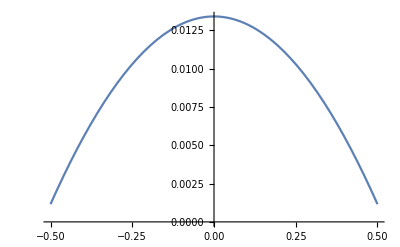

```mathematica
Show[%23,ViewPoint->Front]
```

```mathematica
Plot3D[eigvals,{kx,-π,π},{ky,-π,π},Filling->Bottom,PlotPoints->66,MaxRecursion->3,ImageSize->Large]
```

-Graphics3D-

### Ridgeline plot one dim

```mathematica
eigvals=Eigenvalues[HII[{kx, ky, 0}]/.m->2t]/.{  t->0.05, k0->Pi/2}
```

{γ Cos[kx]-√2 √(0.0125+0.01 Cos[kx]+0.0025 Cos[2 kx]-0.005 Cos[kx-ky]-0.01 Cos[ky]-0.005 Cos[kx+ky]),γ Cos[kx]+√2 √(0.0125+0.01 Cos[kx]+0.0025 Cos[2 kx]-0.005 Cos[kx-ky]-0.01 Cos[ky]-0.005 Cos[kx+ky])}

```mathematica
ListLinePlot3D[
{Table[
First[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, -Pi, Pi, 0.1}
],
Table[
Last[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, -Pi, Pi, 0.1}
]
},
Filling->Axis
]
```

-Graphics3D-

```mathematica
Subdivide[0.15, 3]
```

{0.,0.05,0.1,0.15}

```mathematica
kxList={-Pi}~Join~Range[-Pi, Pi, 0.1]~Join~{Pi};
bottomBand=Table[
First[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, kxList}
];
topBand=Table[
Last[eigvals]/.{ky->0},
{γ, Subdivide[0.15, 3]},
{kx, kxList}
];
bottomBand[[;;, 1]]=-0.2;
bottomBand[[;;, -1]] =-0.2;
topBand[[;;, 1]]=0.2;
topBand[[;;, -1]] =0.2;
```

```mathematica
Prepend[Flatten[Thread[{bottomBand,topBand}], 1], kxList];
Export["/home/thorvald/Documents/NTNU/10semester/Thesis/data/tightBindModel-topbottom.csv", N[Transpose[%]]]
```

/home/thorvald/Documents/NTNU/10semester/Thesis/data/tightBindModel-topbottom.csv

```mathematica
typeiiBendPlots=Table[
Plot3D[
eigvals,
 {kx, -Pi*1.2, Pi*1.2}, {ky, -Pi, Pi},
PlotPoints->66,MaxRecursion->3,ImageSize->Medium, ColorFunction->"Rainbow", PlotStyle->{Opacity[0.9], Specularity[Red, 200]},
ViewPoint->{0,-4,0.5},Boxed->False, Axes->{True,False,True}
],
{γ,Subdivide[0.15, 3]}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
MapIndexed[Export[
FileNameJoin[{NotebookDirectory[],"typeIIbend"<>ToString[First[#2]]<>".png"}]
, #1, ImageResolution->300]&, typeiiBendPlots]
```

{/home/thorvald/Documents/NTNU/10semester/mathematica/typeIIbend1.png,/home/thorvald/Documents/NTNU/10semester/mathematica/typeIIbend2.png,/home/thorvald/Documents/NTNU/10semester/mathematica/typeIIbend3.png,/home/thorvald/Documents/NTNU/10semester/mathematica/typeIIbend4.png}

```mathematica
eigenvals=Eigenvalues[HII[{kx, ky, 0}]/.m->3 t]/.{  t->0.05, γ->0};
typeiiMoveCrossingPlots=Table[
Plot3D[
eigenvals,
 {kx, -Pi*1.2, Pi*1.2}, {ky, -Pi, Pi},
PlotPoints->66,MaxRecursion->3,ImageSize->Medium, ColorFunction->"Rainbow", PlotStyle->{Opacity[0.9], Specularity[Red, 200]},
ViewPoint->{0,-4,0.5},Boxed->False, Axes->{True,False,True}
],
{k0,Subdivide[Pi/2, 2]}
]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
MapIndexed[Export[
FileNameJoin[{NotebookDirectory[],"typeIImove"<>ToString[First[#2]]<>".png"}]
, #1, ImageResolution->300]&, typeiiMoveCrossingPlots]
```

{/home/thorvald/Documents/NTNU/10semester/mathematica/typeIImove1.png,/home/thorvald/Documents/NTNU/10semester/mathematica/typeIImove2.png,/home/thorvald/Documents/NTNU/10semester/mathematica/typeIImove3.png}

## R&D

### Linearization

```mathematica
eigvals=Eigenvalues[HII[{kx, ky, kz}]]
```

{1/2 (-2 γ Cos[k0]+2 γ Cos[kx]-√2 √(10 m^2+16 t^2+16 m t Cos[k0]+4 t^2 Cos[2 k0]-8 t^2 Cos[k0-kx]-16 m t Cos[kx]+4 t^2 Cos[2 kx]-8 t^2 Cos[k0+kx]-4 m t Cos[k0-ky]+4 m t Cos[kx-ky]-8 m^2 Cos[ky]+m^2 Cos[2 ky]-4 t^2 Cos[2 ky]-4 m t Cos[k0+ky]+4 m t Cos[kx+ky]-4 m t Cos[k0-kz]+4 m t Cos[kx-kz]+2 m^2 Cos[ky-kz]-8 m^2 Cos[kz]+m^2 Cos[2 kz]-4 t^2 Cos[2 kz]-4 m t Cos[k0+kz]+4 m t Cos[kx+kz]+2 m^2 Cos[ky+kz])),1/2 (-2 γ Cos[k0]+2 γ Cos[kx]+√2 √(10 m^2+16 t^2+16 m t Cos[k0]+4 t^2 Cos[2 k0]-8 t^2 Cos[k0-kx]-16 m t Cos[kx]+4 t^2 Cos[2 kx]-8 t^2 Cos[k0+kx]-4 m t Cos[k0-ky]+4 m t Cos[kx-ky]-8 m^2 Cos[ky]+m^2 Cos[2 ky]-4 t^2 Cos[2 ky]-4 m t Cos[k0+ky]+4 m t Cos[kx+ky]-4 m t Cos[k0-kz]+4 m t Cos[kx-kz]+2 m^2 Cos[ky-kz]-8 m^2 Cos[kz]+m^2 Cos[2 kz]-4 t^2 Cos[2 kz]-4 m t Cos[k0+kz]+4 m t Cos[kx+kz]+2 m^2 Cos[ky+kz]))}

```mathematica
eigvals/.{kx->kx+k0}
```

{1/2 (-2 γ Cos[k0]+2 γ Cos[k0+kx]-√2 √(10 m^2+16 t^2+16 m t Cos[k0]+4 t^2 Cos[2 k0]-8 t^2 Cos[kx]-16 m t Cos[k0+kx]+4 t^2 Cos[2 (k0+kx)]-8 t^2 Cos[2 k0+kx]-4 m t Cos[k0-ky]+4 m t Cos[k0+kx-ky]-8 m^2 Cos[ky]+m^2 Cos[2 ky]-4 t^2 Cos[2 ky]-4 m t Cos[k0+ky]+4 m t Cos[k0+kx+ky]-4 m t Cos[k0-kz]+4 m t Cos[k0+kx-kz]+2 m^2 Cos[ky-kz]-8 m^2 Cos[kz]+m^2 Cos[2 kz]-4 t^2 Cos[2 kz]-4 m t Cos[k0+kz]+4 m t Cos[k0+kx+kz]+2 m^2 Cos[ky+kz])),1/2 (-2 γ Cos[k0]+2 γ Cos[k0+kx]+√2 √(10 m^2+16 t^2+16 m t Cos[k0]+4 t^2 Cos[2 k0]-8 t^2 Cos[kx]-16 m t Cos[k0+kx]+4 t^2 Cos[2 (k0+kx)]-8 t^2 Cos[2 k0+kx]-4 m t Cos[k0-ky]+4 m t Cos[k0+kx-ky]-8 m^2 Cos[ky]+m^2 Cos[2 ky]-4 t^2 Cos[2 ky]-4 m t Cos[k0+ky]+4 m t Cos[k0+kx+ky]-4 m t Cos[k0-kz]+4 m t Cos[k0+kx-kz]+2 m^2 Cos[ky-kz]-8 m^2 Cos[kz]+m^2 Cos[2 kz]-4 t^2 Cos[2 kz]-4 m t Cos[k0+kz]+4 m t Cos[k0+kx+kz]+2 m^2 Cos[ky+kz]))}

```mathematica
FullSimplify[%]
```

$Aborted

```mathematica
Series[%30, {kx, 0, 1}, {ky, 0,1}, {kz, 0,1}]//Normal
```

%30

```mathematica
Cos[PlusMinus[k0]+kx]-Cos[k0]
```

-Cos[k0]+Cos[kx+±k0]

```mathematica
Series[%, {kx, 0,1}]//Normal
```

-Cos[k0]+Cos[±k0]-kx Sin[±k0]

```mathematica
FullSimplify[%]
```

-Cos[k0]+Cos[±k0]-kx Sin[±k0]

```mathematica
Refine[%, k0 ∈Reals]
```

-Cos[k0]+Cos[±k0]-kx Sin[±k0]

```mathematica
TrigExpand[%]
```

-Cos[k0]+Cos[±k0]-kx Sin[±k0]

```mathematica
eigvals=Eigenvalues[HII[{kx, ky, 0}]/.{ γ->0.15, m->0.15, t->-0.05}]
```

{1/2 (-0.3 Cos[k0]+0.3 Cos[kx]-√((0.195+0. ⅈ)-0.12 Cos[k0]+0.02 Cos[2 k0]-0.04 Cos[k0-kx]+0.12 Cos[kx]+0.02 Cos[2 kx]-0.04 Cos[k0+kx]+0.06 Cos[k0-ky]-0.06 Cos[kx-ky]-0.18 Cos[ky]+0.025 Cos[2 ky]+0.06 Cos[k0+ky]-0.06 Cos[kx+ky])),1/2 (-0.3 Cos[k0]+0.3 Cos[kx]+√((0.195+0. ⅈ)-0.12 Cos[k0]+0.02 Cos[2 k0]-0.04 Cos[k0-kx]+0.12 Cos[kx]+0.02 Cos[2 kx]-0.04 Cos[k0+kx]+0.06 Cos[k0-ky]-0.06 Cos[kx-ky]-0.18 Cos[ky]+0.025 Cos[2 ky]+0.06 Cos[k0+ky]-0.06 Cos[kx+ky]))}

```mathematica
tmp[k0_]:=eigvals/.k0->k0
```

```mathematica
Manipulate[
Plot3D[
Eigenvalues[HII[{kx, ky, 0}]/.{ γ->0.15, m->0.15, t->-0.05}]/.k0->x,
 {kx, -Pi, Pi}, {ky, -Pi, Pi}
],
{x, 0, Pi/2}
]
```

```mathematica
Eigenvalues[HII[{kx, 0, 0}]/.{ γ->0, m->0.15, t->-0.05}]/.k0->Pi/6
```

{-0.1 ((√3)/2-1. Cos[kx]),0.1 ((√3)/2-1. Cos[kx])}

```mathematica
Plot[
-0.1((√3)/2-1.Cos[kx]),
 {kx, -0.5, 0.5}
]
```

-Graphics-

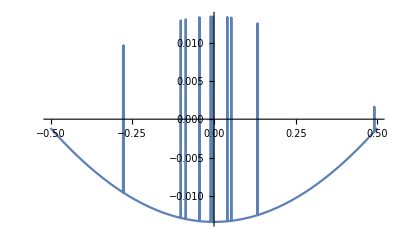

```mathematica
Plot[
(Last[Eigenvalues[HII[{kx, 0, 0}]/.{ γ->0, m->0.15, t->-0.05}]/.k0->Pi/6]),
 {kx, -0.5, 0.5}
]
```

```mathematica
Manipulate[
Plot[
Eigenvalues[HII[{kx, 0, 0}]/.{ γ->g, m->0.15, t->-0.05}]/.k0->x,
 {kx, -Pi, Pi},PlotRange->{-0.4, 0.2}
],
{x, 0, Pi/2},
{g, 0,0.15}
]
```